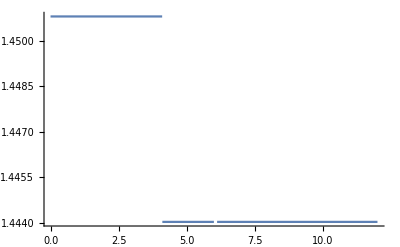

```mathematica
Clear["Global`*"]

silica={{0.6961663,0.0684043},{0.4079426,0.1162414},{0.8974794,9.896161}};
Selmeyer[coeff__]:=Function[{λ},Sqrt[1+Total[#[[1]] λ^2/(λ^2-#[[2]]^2)&/@coeff]]]

dCore=8.2;
NA=0.14;
Window=6.;(*mkm*)
λ=1.55;
β0=2Pi/λ Selmeyer[silica][λ];

CalcWindow=2Window;(*mkm*)
N0=128;
h=10;
N0=N0+Boole[EvenQ[N0]];

n[r_]:=Piecewise[{{Sqrt[Selmeyer[silica][λ]^2+NA^2],0≤r<dCore/2},{Selmeyer[silica][λ],dCore/2≤r<Window},{Selmeyer[silica][λ]-0.001I,Window≤r}}]

Plot[Re[n[r]],{r,0,CalcWindow}]
```

-Graphics-

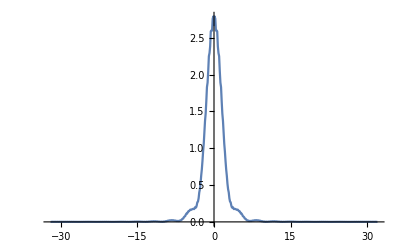

```mathematica
nArr=Array[n[Sqrt[#1^2+#2^2]]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];
StartBeam=Array[Piecewise[{{1,0≤(#1^2+#2^2)<(dCore/2)^2},{0,(dCore/2)^2≤(#1^2+#2^2)}}]&,{N0,N0},{{-CalcWindow,CalcWindow},{-CalcWindow,CalcWindow}}];

D2Fourier=-(Pi/CalcWindow)^2 RotateLeft[Array[(#1^2+#2^2)&,{N0,N0},{-(N0-1)/2,-(N0-1)/2}],{(N0-1)/2,(N0-1)/2}];
FourierOp=Exp[-I/ β0/2 D2Fourier h];
SpatialOp=Exp[-I/2/β0 (2 Pi/λ)^2 (nArr^2-Selmeyer[silica][λ]^2) h];

Beam=InverseFourier[Sqrt[FourierOp]Fourier[StartBeam]];
Monitor[
For[ξ=0.5,ξ<50h,ξ+=h,

Beam=InverseFourier[FourierOp Fourier[Beam SpatialOp]];

],{ξ(*ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->{0,1.5}]*)}]
Beam=InverseFourier[Fourier[Beam]/Sqrt[FourierOp]];

ArrayPlot[Abs[Beam]^2,DataRange->All,ColorFunction->"SunsetColors"]
ListPlot[Abs[Beam[[(N0+1)/2]]]^2,Joined->True,DataRange-> {-CalcWindow,CalcWindow},PlotRange->All]
```

Домашнее задание
1) Найти установившийся пучок в волокне (моду). Параметры волокна приведены в задаче.Подобрать оптимальный шаг дискретизации по z, по пространству и по Фурье-пространству (чем определяется?) для обеспечения приемлемой сходимости метода.
2) Замоделировать следующую задачу: к выходному волокну (SMF-28) приварена наварка (кварцевый цилиндр) диаметром 30 мкм длины L.
Построить график распределения интенсивности в пучке на выходе из наварки. (Одномерный, по радиусу)
Построить график распределения интенсивности дифрагированного излучения в дальней зоне в координатах (θ, I). (Одномерный, по радиусу)
Вычислить M2 параметр качества пучка. (M2 - отношение среднеквадратичного угла расходимости пучка к расходимости гауссова пучка с такой же среднеквадратичной шириной. Можно использовать функцию Moment) 
Найти длину наварки L, при которой M2 портится в два раза.